## Kerbin Ascent Stuff

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/kids/Documents/Physics 230

```mathematica
kerbinPressureDataRawPascals=Import["kerbin_altitude_vs_pressure.csv"];
```

```mathematica
kpdataKPascals=Delete[kerbinPressureDataRawPascals,1];
```

```mathematica
kpdataPascals=kpdataKPascals/.{h_,p_}->{h,(p*1000)};
```

```mathematica
kpequation[h_]=Interpolation[kpdataPascals,h];
```

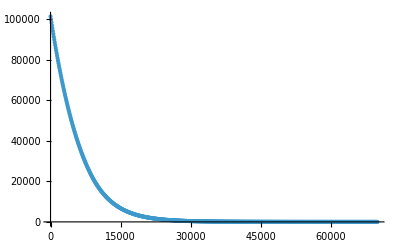

```mathematica
ListPlot[kpdataPascals,PlotRange->All]
```

```mathematica
exponentialFitEquation=(k)/(1+A*E^(-r*h));
```

```mathematica
pressureFit=FindFit[kpdataPascals,exponentialFitEquation,{k,A,r},h]
```

{k→8427.76,A→-1.63192×10^6,r→2.66993×10^44}

```mathematica
pressureFitEquation=exponentialFitEquation/.pressureFit
```

8427.76/(1-1.63192×10^6 ⅇ^(-2.66993×10^44 h))

```mathematica
kpequation[15006]
```

6.71429

### This equation does effectively nothing, but was supposed to predict ascent assuming no drag and constant gravity.

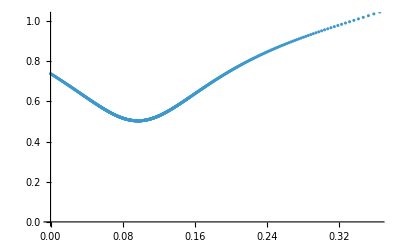

```mathematica
ascentProfileNoDrag[ti_,tf_,ψi_,vi_,xi_,yi_,n_Function,g_]:=Module[{ψ,Δψ,z0,ψ0,c,z,v,t,Δt,x,x0,Δx,y,y0,Δy,xytvψdata,xt,yt,xy,vt,ψt},
Δψ=ψi/100;ψ0=ψi;x0=xi;y0=yi;t=ti;xytvψdata={};
While[t<tf,
z0=-Tan[0.5ψ0];
c=-vi/(((-z0)^(n[t]-1))((1+(-z0))^2));
ψ=-(ψ0+Δψ);
z=-Tan[0.5(-ψ)];
v=(-c)*((-z)^(n[t]-1))*(1+((-z)^2));
Δt=((-c)/g)*((((-z)^(n[t]-1))*((1/(n[t]-1))+(((-z)^2)/(n[t]+1))))-(((-z0)^(n[t]-1))*((1/(n[t]-1))+(((-z0)^2)/(n[t]+1)))));
Δx=(0.5)*((vi*Sin[ψ0])+(v*Sin[(-ψ)]))*(Δt);
Δy=(0.5)*((vi*Sin[ψ0])+(v*Sin[(-ψ)]))*(Δt);
x=x0+Δx;y=y0+Δy;
x0=x;y0=y;ψ0=-ψ;
AppendTo[xytvψdata,{x,y,t,v,ψ0}];
t=t+Δt
];
xt=xytvψdata/.{x_,y_,t_,v_,ψ_}->{t,x};
yt=xytvψdata/.{x_,y_,t_,v_,ψ_}->{t,y};
xy=xytvψdata/.{x_,y_,t_,v_,ψ_}->{x,y};
vt=xytvψdata/.{x_,y_,t_,v_,ψ_}->{t,v};
ψt=xytvψdata/.{x_,y_,t_,v_,ψ_}->{t,ψ};
ListPlot[vt]
];
ascentProfileNoDrag[0,60,(Pi/8),1,0,68,(3E^(-5*#))&,9.81]
```

```mathematica
ascentProfileNoDrag[0,1000,15Degree,500,0,3000,(3E^(-5*#))&,32.174]
```

-Graphics-

### This is the equation that describes thrust of the Swivel rocket by altitude.

```mathematica
swivelThrustData={{0,167968.75},{79,168414},{83,168437},{103,168554},{164,168910},{337,169931},{492,170835},{868,173017},{1007,173818},{1457,176344},{1548,176848},{2011,179354},{2532,182055},{3005,184393},{3618,187252},{4080,189281},{4669,191706},{5101,193374},{5549,195002},{6030,196646},{7039,199746},{8119,202581},{8914,204382},{9938,206344},{11115,208150},{11816,209039},{12906,210198},{13578,210796},{14047,211168},{14997,211825},{16106,212447},{17130,212912},{18581,213427},{20207,213849},{22173,214208},{23507,214386},{25801,214599},{27315,214695},{29155,214781},{31988,214866},{33787,214900},{36138,214932},{39336,214959},{39750,214962},{41479,214970},{43180,214977},{45647,214985},{48711,214991},{52243,214995},{55163,214997},{59254,214999},{63425,214999},{66987,215000},{68982,215000},{70000,215000}};
```

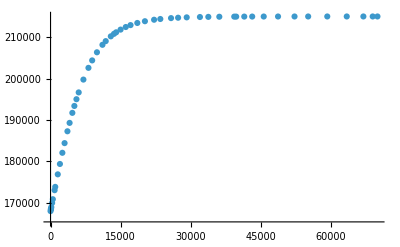

```mathematica
ListPlot[swivelThrustData]
```

```mathematica
swivelThrust[h_]:=Interpolation[swivelThrustData,h]
```

```mathematica
swivelThrust[4988]
```

192947.

```mathematica
swivelFit=FindFit[swivelThrustData,exponentialFitEquation,{k,A,r},h]
```

{k→201451.,A→-1.80789×10^8,r→2.24232×10^34}

```mathematica
swivelThrustEquation=exponentialFitEquation/.swivelFit
```

201451./(1-1.80789×10^8 ⅇ^(-2.24232×10^34 h))

### “Mite” Solid Fuel Booster

With Mk1 Command Pod and 1 astronaut

/Users/antanner/Documents/phscs230/moar-boosters

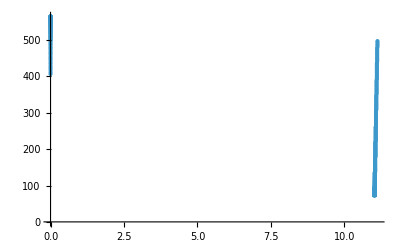

```mathematica
SetDirectory[NotebookDirectory[]]
miteData = Import["rocket_data/mite_12150925.csv", "Data"];
thrustAltitudeMiteData=miteData[[All,{5,14}]];
ListPlot[thrustAltitudeMiteData]
```

### “Spark” Liquid Fuel Engine

With FL-T100 Fuel Tank, Mk1 Command Pod, and 1 astronaut

/Users/antanner/Documents/phscs230/moar-boosters

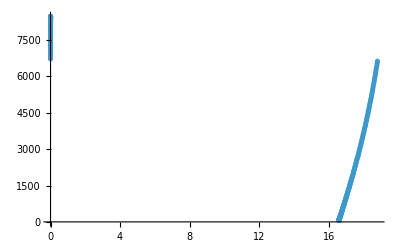

```mathematica
SetDirectory[NotebookDirectory[]]
miteData = Import["rocket_data/spark_12150946.csv", "Data"];
thrustAltitudeMiteData=miteData[[All,{5,14}]];
ListPlot[thrustAltitudeMiteData]
```

## For vertical flight, single stage

### With u being proportionate to specific impulse:

```mathematica
u[g_,i_]:=g*i;
vmax[u_,mi_,mbo_,g_,tbo_,vi_,i_]:=(-u*Log[mi/mbo]-(g*tbo))+vi;
```

### More clearly:

```mathematica
tr[thrust_,mi_,g_]:=thrust/(mi*g);
vburnout[vi_,mi_,mf_,g_,i_,thrust_]:=((g*i)(Log[mi/mf]-((1/tr[thrust,mi,g])*(1-(mf/mi)))))+vi;
```

### Integrating for distance traveled:

```mathematica
hburnout[gi_,i_,thrust_,mi_,mf_,vi_]:=((gi)((i^2)/(tr[thrust,mi,gi]^2))(1-((1/((mi/mf)-1))(Log[mi/mf]))))+((vi)(1/tr[thrust,mi,gi])(1-(mf/mi)))-((1/2)(gi)((i^2)/(tr[thrust,mi,gi]^2))((1-(mf/mi))^2));
rburnout[gi_,i_,thrust_,mi_,mf_,vi_,rlaunch_]:=rlaunch+hburnout[gi,i,thrust,mi,mf,vi];
hcoast[vi_,mi_,mf_,g_,i_,thrust_,rlaunch_]:=((vburnout[vi,mi,mf,g,i,thrust]^2)/(2g))((rburnout[g,i,thrust,mi,mf,vi,rlaunch]^2)/((rlaunch^2)-(((vburnout[vi,mi,mf,g,i,thrust]^2)/(2g))(rburnout[g,i,thrust,mi,mf,vi,rlaunch]))));
htotal[g_,i_,thrust_,mi_,mf_,vi_,rlaunch_]:=hburnout[g,i,thrust,mi,mf,vi]+hcoast[vi,mi,mf,g,i,thrust,rlaunch];
```

### These numbers should predict a small vertical flight, but ended up predicting numbers too high, which don’t account for drag.

The top altitude reached ended up being 10931 and the max speed was 454 m/s

```mathematica
htotal[9.81,250,167968,3755,2955,0,600068]/1000
```

14.4534

```mathematica
vburnout[0,3755,2955,9.81,250,167968]
```

473.005

## Predictions

### Mite w/ Full Fuel

```mathematica
htotal[9.81,190,11212,485,185,0,600068]
vburnout[0,485,185,9.81,190,11212]
```

120652.

1307.17

The max altitude reached was 104,855 meters, and the max velocity reached was 1173 m/s.

### Mite w/ Quarter Fuel

```mathematica
htotal[9.81,185,11012,260,185,0,600068]
vburnout[0,260,185,9.81,185,11012]
```

15061.7

496.384

The max altitude reached was 6781 meters, and the max velocity reached was 395 m/s.

### Spark w/ Half Fuel

```mathematica
htotal[9.81,265,16563,1595,1095,0,600068]
vburnout[0,1595,1095,9.81,265,16563]
```

81008.3

207.913

The max altitude reached was 6683 meters, and the max velocity reached was 228 m/s.

### Spark Mini

```mathematica
htotal[9.81,265,16563,435,235,0,600068]
vburnout[0,435,235,9.81,265,16563]
```

109913.

1292.82

The max altitude reached was 59436 meters, and the max velocity reached was 1100 m/s.